```mathematica
Integrate[x^(z-1)Exp[-x],{x,0,∞}]
```

ConditionalExpression[Gamma[z],Re[z]>0]

```mathematica
Integrate[f[z]Exp[-x],{x,0,∞}]
```

f[z]

```mathematica
(1+Cos[π x])/2
```

1/2 (1+Cos[π x])

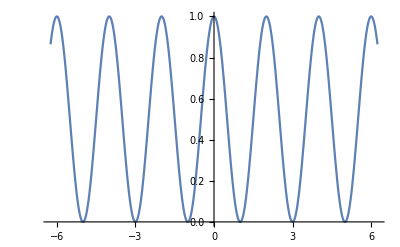

```mathematica
Plot[1/2 (1+Cos[π x]),{x,-6.24,6.24}]
```

```mathematica
(1-(1/2 (1+Cos[π x])))(3x+1)+(1/2 (1+Cos[π x]))(x/2)
```

(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x])

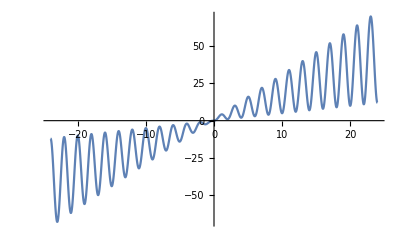

```mathematica
Plot[(1+3 x) (1+1/2 (-1-Cos[π x]))+1/4 x (1+Cos[π x]),{x,-24.,24.}]
```

```mathematica
Integrate[(1+3 x) (1+1/2 (-1-Cos[π z]))+1/4 x (1+Cos[π z])Exp[-x],{x,0,∞}]
```

Integrate::idiv: Integral of 1/2+(3 x)/2+(ⅇ^-x x)/4-1/2 Cos[π z]-3/2 x Cos[π z]+1/4 ⅇ^-x x Cos[π z] does not converge on {0,∞}.

∫_0^∞ ((1+3 x) (1+1/2 (-1-Cos[π z]))+1/4 ⅇ^-x x (1+Cos[π z]))ⅆx

```mathematica
Integrate[(1+3 z) (1+1/2 (-1-Cos[π x]))+1/4 z (1+Cos[π x])Exp[-x],{x,0,∞}]
```

Integrate::idiv: Integral of 1/2+(3 z)/2+(ⅇ^-x z)/4-1/2 Cos[π x]-3/2 z Cos[π x]+1/4 ⅇ^-x z Cos[π x] does not converge on {0,∞}.

∫_0^∞ ((1+3 z) (1+1/2 (-1-Cos[π x]))+1/4 ⅇ^-x z (1+Cos[π x]))ⅆx

```mathematica
InverseMellinTransform[Gamma[x+1],x,s]
```

ⅇ^-s s